```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zack/Documents/rmtchem

## Regular random matrices

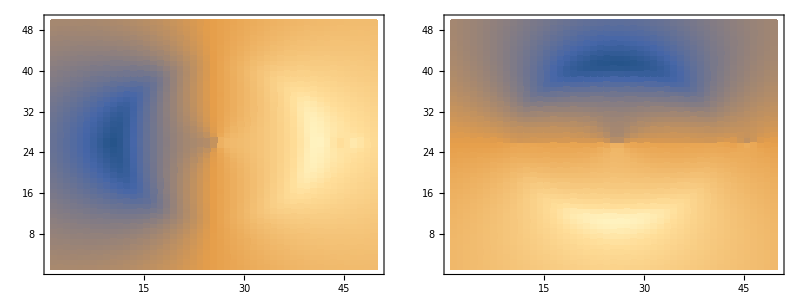

InterpolatingFunction[…]

InterpolatingFunction[…]

-Graphics-

```mathematica
test1=Partition[Partition[Partition[BinaryReadList["data/2_100g.npy","Complex128"][[9;;-1]],2],2],50];Grid[{{ListDensityPlot[Transpose[Re[test[[All,All,2,1]]]],ImageSize->300,InterpolationOrder->0],
ListDensityPlot[Transpose[Im[test[[All,All,2,1]]]],ImageSize->300,InterpolationOrder->0]}}]
gr=Interpolation[Flatten[Table[{-5+10/49*(i-1),-5+10/49*(j-1),Re[test[[i,j,2,1]]]},{i,1,50},{j,1,50}],1]]
gi=Interpolation[Flatten[Table[{-5+10/49*(i-1),-5+10/49*(j-1),Im[test[[i,j,2,1]]]},{j,1,50},{i,1,50}],1]]

c2=Partition[BinaryReadList["data/2_100.npy","Real64"][[17;;-1]],101];
Grid[{{ListDensityPlot[Transpose[c2],InterpolationOrder->1,ImageSize->300,InterpolationOrder->0],DensityPlot[Evaluate[D[gr[x,y],x]-D[gi[x,y],y]],{x,-5,5},{y,-5,5},ImageSize->300]}}]
```

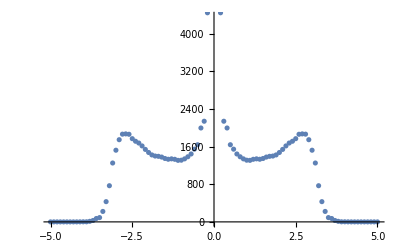

```mathematica
ListPlot[Table[{Y,Evaluate[D[gr[x,y],x]-D[gi[x,y],y]]}/.{x->0,y->Y},{Y,-5,5,0.1}]]
```

{25,100,2,2}

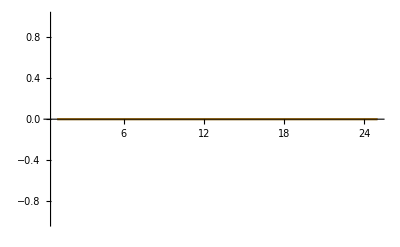

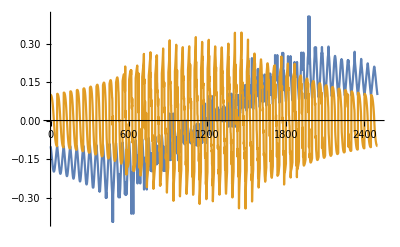

-Graphics-

```mathematica
grvals=Partition[Partition[Partition[BinaryReadList["data/testgr.npy","Complex128"][[9;;-1]],2],2],100];
gvals=Partition[Partition[BinaryReadList["data/testg.npy","Complex128"][[9;;-1]],2],2];
Dimensions[grvals]
ListPlot[Sum[{Re[grvals[[All,i,2,1]]],Im[grvals[[All,i,2,1]]]},{i,1,100}]/100,Joined->True,PlotRange->All]
ListPlot[{Re[gvals[[All,2,1]]],Im[gvals[[All,2,1]]]},Joined->True,PlotRange->All]
c2=Partition[BinaryReadList["data/2_100.npy","Real64"][[17;;-1]],101];
ListDensityPlot[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All]
```

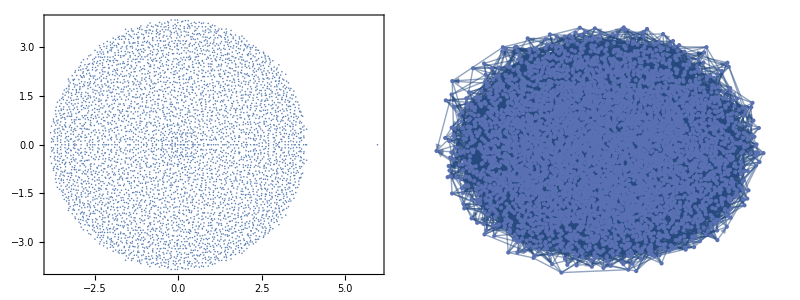

{3,3}

{3,3}

graph1.pdf

```mathematica
mat=BinaryReadList["data/3/1mat.npy","Real64"][[17;;-1]];
n=Length[mat]^(1/2);
mat=Partition[mat,n];
evals=Partition[BinaryReadList["data/3/1evals.npy","Real64"][[17;;-1]],2];
Grid[{{ListPlot[evals,ImageSize->300,AspectRatio->1,Axes->False,Frame->True,LabelStyle->Directive[16]],GraphPlot[AdjacencyGraph[mat/.u_/;Abs[u]>0->1],ImageSize->300]}}]
{Min[#],Max[#]}&@(Count[#,u_/;u≠0.]&/@mat)
{Min[#],Max[#]}&@(Count[#,u_/;u≠0.]&/@Transpose[mat])
Export["graph1.pdf",GraphPlot[AdjacencyGraph[mat/.u_/;Abs[u]>0->1],ImageSize->300]]
```

```mathematica
offset
scale
```

0.

5.4

```mathematica
c2=BinaryReadList["data/2_50.npy","Real64"][[17;;-1]];
c2=Transpose[Partition[c2,Length[c2]^(1/2)]];
scale=Max[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]]/1;
offset=0.0*Median[Cases[Flatten[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]],u_/;u>10]];
cf=If[#<1,White,ColorData["M10DefaultDensityGradient"][(#-offset)/(scale-offset)]]&;
Rasterize[ListDensityPlot[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300]
```

-Graphics-

```mathematica
c2=BinaryReadList["data/2.npy","Real64"][[17;;-1]];
c2=Transpose[Partition[c2,Length[c2]^(1/2)]];
c3=BinaryReadList["data/3.npy","Real64"][[17;;-1]];
c3=Transpose[Partition[c3,Length[c3]^(1/2)]];
c4=BinaryReadList["data/4.npy","Real64"][[17;;-1]];
c4=Transpose[Partition[c4,Length[c4]^(1/2)]];
c5=BinaryReadList["data/5.npy","Real64"][[17;;-1]];
c5=Transpose[Partition[c5,Length[c5]^(1/2)]];

scale=Max[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]]/10;
offset=0.3*Median[Cases[Flatten[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]],u_/;u>100]];
cf=If[#<1,White,ColorData["M10DefaultDensityGradient"][(#-offset)/(scale-offset)]]&;
AbsoluteTiming[{raster2,raster3,raster4,raster5}={Rasterize[ListDensityPlot[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300],Rasterize[ListDensityPlot[Join[c3[[1;;Floor[Length[c3]/2]]],c3[[Floor[Length[c3]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300],Rasterize[ListDensityPlot[Join[c4[[1;;Floor[Length[c4]/2]]],c4[[Floor[Length[c4]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300],Rasterize[ListDensityPlot[Join[c5[[1;;Floor[Length[c5]/2]]],c5[[Floor[Length[c5]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300]};]
p=Rasterize[Plot3D[{0,2,4,6},{x,-10,10},{y,-10,10},Mesh->None,PlotRange->{{-8,8},{-8,8},{0,6}},PlotStyle->{Directive[Texture[raster2]],Directive[Texture[raster3]],Directive[Texture[raster4]],Directive[Texture[raster5]]},Lighting->{"Ambient",White},Boxed->False,Axes->False,Background->None,ImageSize->300,ViewPoint->{-12,0,2},AspectRatio->2,ViewAngle->0.065],ImageResolution->300];
Rotate[p,-Pi/2]
Export["stack.png",Rotate[p,-Pi/2]]
```

{563.673,Null}

-Graphics-

stack.png

```mathematica
c2=BinaryReadList["data/2.npy","Real64"][[17;;-1]];
c2=Transpose[Partition[c2,Length[c2]^(1/2)]];

scale=Max[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]]/10;
offset=0.3*Median[Cases[Flatten[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]],u_/;u>100]];
cf=If[#<1,White,ColorData["M10DefaultDensityGradient"][(#-offset)/(scale-offset)]]&;

p=Rasterize[ListDensityPlot[Join[c2[[1;;Floor[Length[c2]/2]]],{c2[[Floor[Length[c2]/2]]]+c2[[2+Floor[Length[c2]/2]]]}/2,c2[[Floor[Length[c2]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->{{100,400},{100,400}},Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300]
Export["spectrum.png",p]
```

-Graphics-

spectrum.png

## Chemical reaction networks

data/test

{100,500}

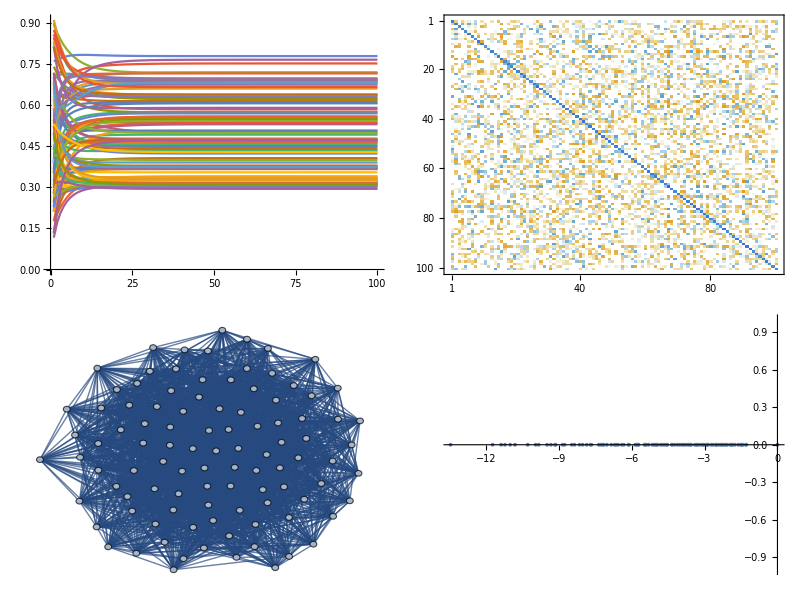

```mathematica
filebase="data/test"
{n,nr}=Import[filebase<>"out.dat"][[1]]
X=Transpose[Partition[BinaryReadList[filebase<>"X.npy","Real64"][[17;;-1]],n]];
nu=Partition[BinaryReadList[filebase<>"nu.npy","Real64"][[17;;-1]],n];
eta=Partition[BinaryReadList[filebase<>"eta.npy","Real64"][[17;;-1]],n];
mat=Partition[BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]],n];
adj=mat/.u_/;Abs[u]>0->1/.(0.)->0;
Grid[{{ListPlot[X,PlotRange->All,Joined->True,ImageSize->300],MatrixPlot[mat,ImageSize->300]},{AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300],ListPlot[{Re[#],Im[#]}&/@Eigenvalues[mat],ImageSize->300]}}]
```

data/irreversible2

{100,250}

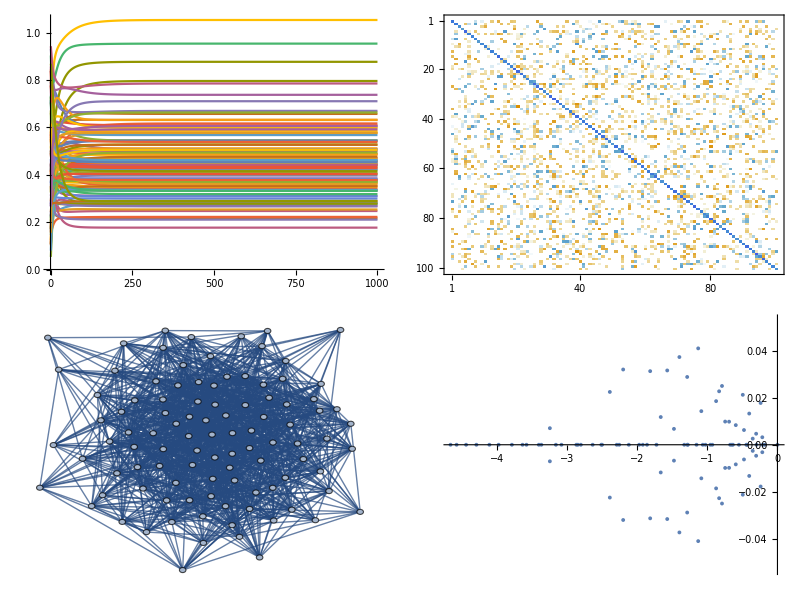

graph2.pdf

```mathematica
filebase="data/irreversible2"
{n,nr}=Import[filebase<>"out.dat"][[1]]
X=Transpose[Partition[BinaryReadList[filebase<>"X.npy","Real64"][[17;;-1]],n]];
nu=Partition[BinaryReadList[filebase<>"nu.npy","Real64"][[17;;-1]],n];
eta=Partition[BinaryReadList[filebase<>"eta.npy","Real64"][[17;;-1]],n];
mat=Partition[BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]],n];
adj=mat/.u_/;Abs[u]>0->1/.(0.)->0;
Grid[{{ListPlot[X,PlotRange->All,Joined->True,ImageSize->300],MatrixPlot[mat,ImageSize->300]},{AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300],ListPlot[{Re[#],Im[#]}&/@Eigenvalues[mat],ImageSize->300]}}]
Export["graph2.pdf",AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300]]
```

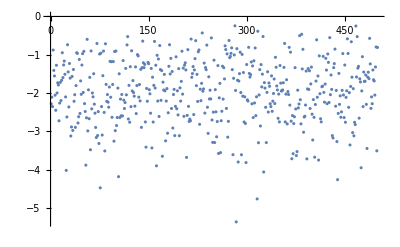

```mathematica
ListPlot[Diagonal[mat]]
```

```mathematica
filebase="data/irreversible2"
{n,nr}=Import[filebase<>"out.dat"][[1]]
X=Transpose[Partition[BinaryReadList[filebase<>"X.npy","Real64"][[17;;-1]],n]];
nu=Partition[BinaryReadList[filebase<>"nu.npy","Real64"][[17;;-1]],n];
eta=Partition[BinaryReadList[filebase<>"eta.npy","Real64"][[17;;-1]],n];
mat=Partition[BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]],n];
adj=mat/.u_/;Abs[u]>0->1/.(0.)->0;
Grid[{{ListPlot[X,PlotRange->All,Joined->True,ImageSize->300],MatrixPlot[mat,ImageSize->300]},{AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300],ListPlot[{Re[#],Im[#]}&/@Eigenvalues[mat],ImageSize->300]}}]
```

data/irreversible2

{100,250}

-Graphics-